```mathematica
res={61,245,981,3926,15707};
```

```mathematica
nh={4.98135,5.35031,6.60889,5.81415,5.92122};
```

```mathematica
nhdir={2.30283,2.14463,2.10712,2.09761,2.09519};
```

```mathematica
qbend={1.31255,1.30319,1.30525,1.31781,1.32014};
```

```mathematica
nhdata=Table[{res[[i]],nh[[i]]},{i,1,Length[res]}];
```

```mathematica
nhdrdata=Table[{res[[i]],nhdir[[i]]},{i,1,Length[res]}];
```

```mathematica
qbenddata=Table[{res[[i]],qbend[[i]]},{i,1,Length[res]}];
```

```mathematica
exact=2.0944;
```

```mathematica
exactdata=Table[{res[[i]],exact},{i,1,Length[res]}];
```

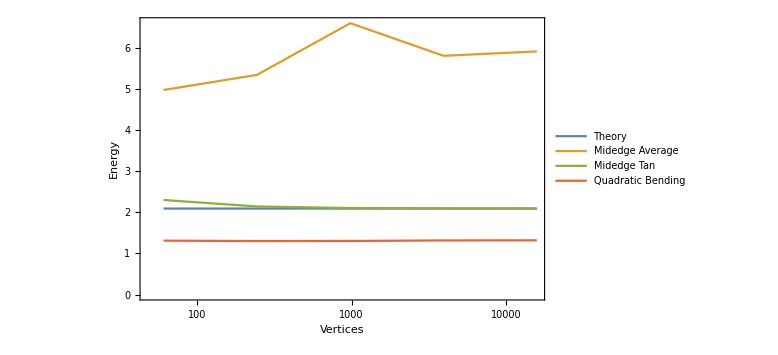

```mathematica
plt=ListLogLinearPlot[{exactdata,nhdata,nhdrdata,qbenddata},Joined->True,PlotStyle->Thick,Frame->True,LabelStyle->{FontSize->12},ImageSize->Large,PlotLegends->{"Theory","Midedge Average","Midedge Tan","Quadratic Bending"},FrameLabel->{"Vertices","Energy"}]
```

```mathematica
Export["sphereplt.png",plt]
```

sphereplt.png